# The silicon fcc crystal structure using DFTB+

In this nb we are going to compute the ground state of the silicon fcc crystal using DFTB+, and then we will compute the electronic structure.

## Convergency of k - points

-Graphics- that k

the convergency criteia is <1meV/atom.

let’s see one output 
-Graphics-

that are the kpoints, in fractional space

```mathematica
SetDirectory["/home/angeldavid/wrk/session2/session2/"];
```

```mathematica
file="kp.dat"
```

kp.dat

```mathematica
kpdat=Import[file]
```

{{4,-92.8995},{5,-92.8972},{6,-92.8994},{7,-92.8992},{8,-92.8994},{9,-92.8994},{10,-92.8994},{11,-92.8994},{12,-92.8994},{13,-92.8994}}

this is the enrgy, but i  need energy per atom (divide eneryg / 2) we have 2 atoms

```mathematica
kpdat=Import[file]//Map[#/{1,2}&,#]&
```

{{4,-46.4498},{5,-46.4486},{6,-46.4497},{7,-46.4496},{8,-46.4497},{9,-46.4497},{10,-46.4497},{11,-46.4497},{12,-46.4497},{13,-46.4497}}

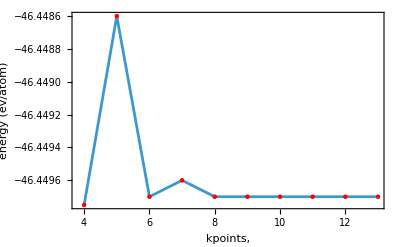

```mathematica
ListPlot[kpdat,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"kpoints,","energy (ev/atom)"}]
```

We have to check the convergence of this caltulation.

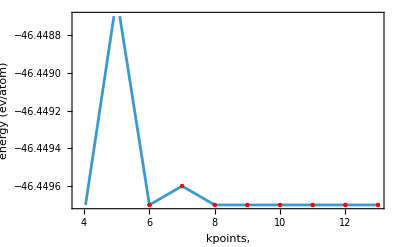

```mathematica
ListPlot[kpdat,
PlotRange->{kpdat[[-1,2]],kpdat[[-1,2]]+10^-3},
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"kpoints,","energy (ev/atom)"}]
```

We get <1 meV/atom convergency

## Equation of states for Si - fcc using DFTB +

```mathematica
SetDirectory["/home/angeldavid/wrk/session2/session2/eos/"];
```

```mathematica
Range[5.23,5.59,0.02]
```

{5.23,5.25,5.27,5.29,5.31,5.33,5.35,5.37,5.39,5.41,5.43,5.45,5.47,5.49,5.51,5.53,5.55,5.57,5.59}

```mathematica
datacell=Import["cell.dat"];
```

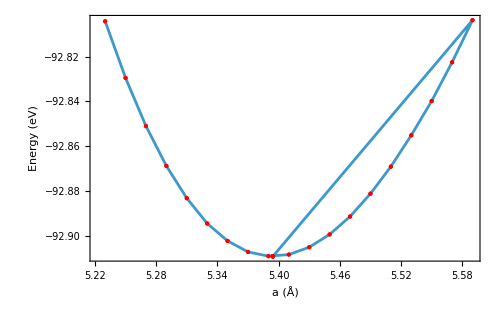

```mathematica
ListPlot[datacell,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"a (Å)","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImageSize->500
]
```

We need to transform the data to volume vs energy. For the Si-fcc based on the POSCAR we have this:

```mathematica
a1=a{1/2,1/2,0.0};
a2=a{0,1/2,1/2};
a3 =a{1/2,0,1/2};
```

Then the volume of the cell is:

```mathematica
a1.(a2×a3)
```

0.+a^3/4

```mathematica
cell = datacell//Map[{(#[[1]])^3/4,#[[2]]}&,#]&
```

{{35.7639,-92.8042},{36.1758,-92.8295},{36.5908,-92.851},{37.009,-92.8688},{37.4303,-92.8832},{37.8549,-92.8945},{38.2826,-92.9023},{38.7135,-92.9072},{39.1477,-92.9091},{39.5851,-92.9084},{40.0258,-92.9051},{40.4697,-92.8994},{40.9168,-92.8914},{41.3673,-92.8812},{41.821,-92.8691},{42.2781,-92.8551},{42.7385,-92.8398},{43.2022,-92.8225},{43.6692,-92.8037},{39.243,-92.9092},{39.243,-92.9092},{39.243,-92.9092},{39.243,-92.9092}}

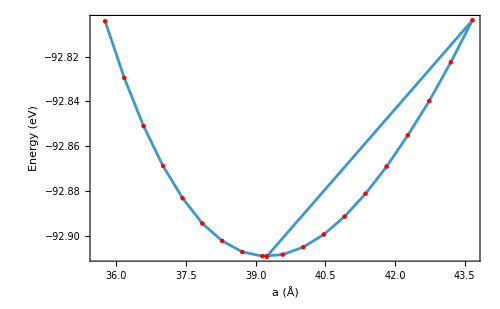

```mathematica
ListPlot[cell,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"a (Å)","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImageSize->500
]
```

Let' s fit data to BM-EOS

```mathematica
e= e0+(9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' +((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)));
```

This is not correct.

```mathematica
e0+(9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' +((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model = k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2
```

k[1]+k[2]/v^(2/3)+k[3]/v^(4/3)+k[4]/v^2

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm = NonlinearModelFit[cell,model,parameters,v];
```

```mathematica
nlm[v]
```

-95.1012+40538.3/v^2-7313.17/v^(4/3)+354.615/v^(2/3)

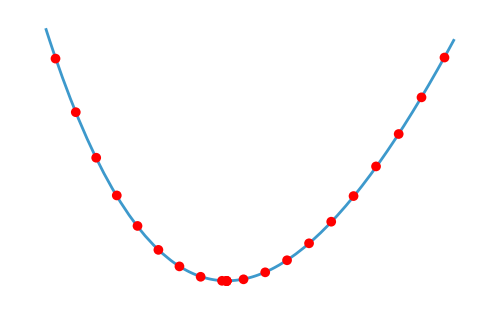

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2,(cell[[All,1]]//Max)+0.2},Epilog->{AbsolutePointSize[7],Red,Point[cell]},
Axes->None,
PlotRange->All,
FrameLabel->{"a (Å)","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImageSize->500
]
```

```mathematica
nlm["RSquared"]
```

1.

Optimal Volume

```mathematica
opvol = FindMinimum[nlm[v],{v,39.1}]
```

{-92.9091,{v→39.2428}}

```mathematica
opvol[[2]]
```

{v→39.2428}

```mathematica
bulkm=v D[nlm[v],{v,2}]/.opvol[[2]]
```

0.546603

The B_0 has units of pressure, here it expresed in units of [eV/Å^3], then in i.u. [N/m^2] =[Pa]:

```mathematica
UnitConvert[Quantity[bulkm,"Electronvolts"/("Angstroms")^3],"GigaPascals"]
```

87.5755 GPa

Now we compute the bulk modulus pressure derivative

```mathematica
bulkpd= -v/bulkm D[v[D[nlm[v],{v,2}],v]]
```

-1.82948 v v[243230./v^4-22752.1/v^(10/3)+394.016/v^(8/3),v]

```mathematica
sol = Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-92.9091,B0→0.546603,v0→39.2428,B'→6.18168},{e0→-89.9047,B0→-0.0200407,v0→161.84,B'→3.15165}}

By looking to the plot of the EOS, we know that v0 is ~39, then the 1st solution is the correct

```mathematica
Solve[v0==a^3/4,a]/.sol[[1]]
```

{{a→-2.69718+4.67165 ⅈ},{a→5.39436},{a→-2.69718-4.67165 ⅈ}}

Finally, the optimal lattie parameter of Si-fcc using DFTB+ is 5.39437 Å

A bulk modulus negative is how much soft is the material, thin about the submarine

## Density of States (DOS) for silicon fcc using DFTB+

```mathematica
SetDirectory["/home/angeldavid/wrk/session2/session2/eos"];
```

```mathematica
dos=Import["dos_totalkp6.dat"];
```

```mathematica
ef=dos[[1,3]]
```

-5.7887

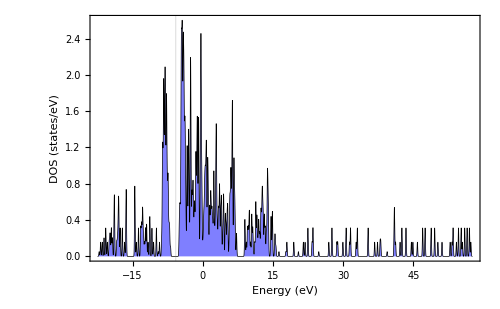

```mathematica
dos=Import["dos_totalkp6.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

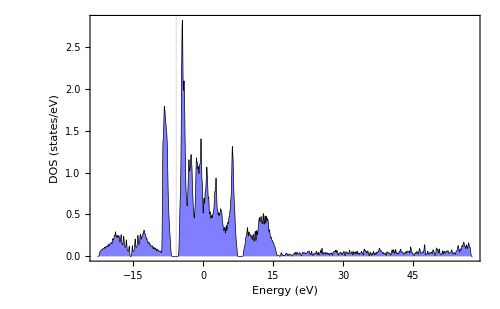

```mathematica
dos=Import["dos_totalkp18.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

Let' s do the calculation with more k points

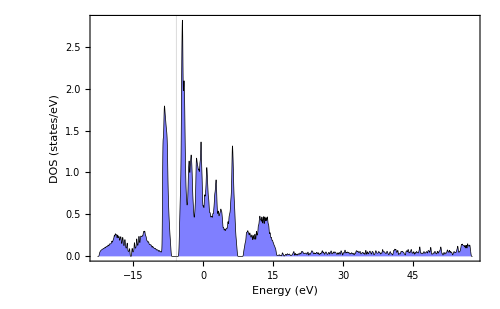

```mathematica
dos=Import["dos_totalkp22.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

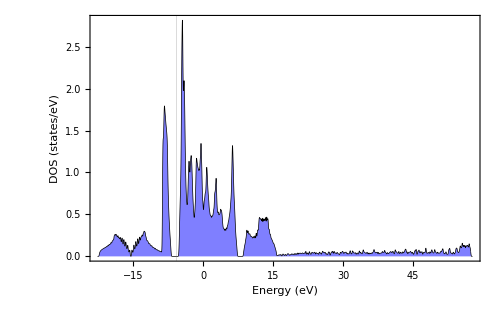

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

Let’s do a zoom around the fermi level

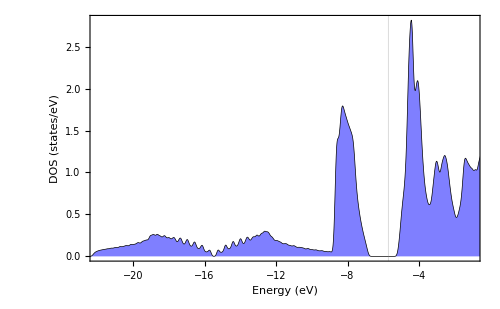

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{{-22,-1},All}

]
```

Here the fermi level is at  zero value dos states eV. Other programs use to put the fermi level at the lowest energy.

The conduction band is empty.

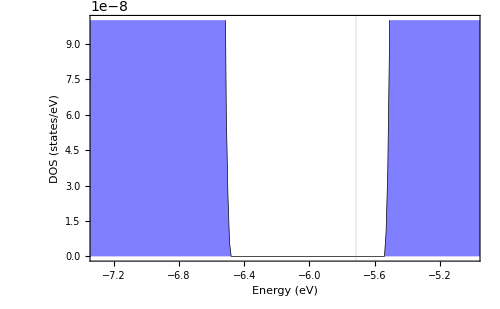

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{{-7.3,-5},{0,10^-7}}

]
```

```mathematica
{{-6.480531830416075,3.5108362174339645*^-10}-{-5.5401886293823015,-4.2681197191020445*^-11}}
```

{{-0.940343,3.93765×10^-10}}

Then  the bandgap or E_g is 0.94 eV. If there is a bandgap this material is an isolator. the left of the fermi level is the valance  and on the right for the bandgap is the conduction band and it is usually empty.

In this case we observe a bandgap around the fermi level, i.e., there are no energy levels near the fermi level, thus the material is isolator.

The density of states is telling me the amount of electronic states we can have high and low concentration of electronic states.

We can check how many valance electrons this system has . For that we integrate the density of states, all the range below the fermi level.  We have in total 8 electrons.

Now let’s compute the partial density of states for Si-fcc using DFTB+.

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
doss=Import["dos_si.s.dat"];
dosp=Import["dos_si.p.dat"];
dosd=Import["dos_si.d.dat"];
```

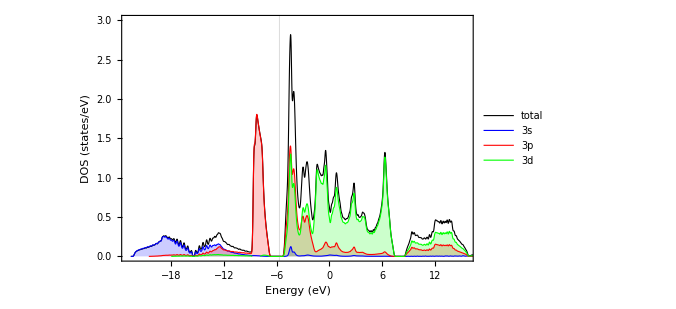

```mathematica
ListPlot[{dos[[2;;-1]],doss,dosp,dosd},
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Filling->{2->Axis,3->Axis,4->Axis},
(*FillingStyle->Directive[Opacity[0.5],Blue],*)
PlotStyle->{{AbsoluteThickness[0.8],Black},{AbsoluteThickness[0.8],Blue},{AbsoluteThickness[0.8],Red},{AbsoluteThickness[0.8],Green}},
ImageSize->500,
PlotLegends->Placed[{"total","3s","3p","3d"},{Scaled[{0,0.75}],{0,0.5}}],
PlotRange->{{-22.9,15.6},{0,3}}

]
```

Here add analysis of the PDOS.

## The Band Structure of Si-fcc using DFTB+

From the SeekPath website, we can compute the first BZ using the optimal POSCAR from the computed ground

We are going to compute the band structure along L→Γ→X→K→W→Γ. For this use the script band_tot.dat that will generate the file band_tot.dat

```mathematica
SetDirectory["/home/angeldavid/wrk/session2/session2/eos"];
```

```mathematica
databands=Import["band_tot.dat"];
```

Then we need the fermi level for that

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
```

```mathematica
databands//Dimensions
```

{101,19}

In the high simmetry paths, There is 19 bands-energy levels (ϵ_nk), 101 are the divisions , remember we put 1,20,20,20,20 at the beguining of the path (it is the discretization of the k axis)in the xbands.sh

```mathematica
databands[[1]] (*these are the energy levels for k=1*)
```

{1,-18.979,-12.444,-7.619,-7.619,-4.311,-4.191,-4.191,-0.846,-0.419,-0.419,0.252,0.252,7.355,7.355,13.923,13.923,20.778,41.935}

```mathematica
databands[[2]] (*and so on for k =101*)
```

{2,-19.018,-12.4,-7.615,-7.615,-4.313,-4.195,-4.195,-0.848,-0.498,-0.498,0.352,0.352,7.337,7.337,13.934,13.934,20.745,41.697}

```mathematica
databands[[-1]] (*and this is the last k point k=101*)
```

{101,-22.279,-6.836,-6.836,-6.836,-5.182,-5.182,-5.182,-1.567,-1.567,2.509,2.509,2.509,6.874,6.874,8.385,15.747,15.747,15.747}

```mathematica
bands = databands//Map[#[[2;;-1]]-ef&,#]&//Transpose;
```

```mathematica
bands[[1]]
```

{-13.2647,-13.3037,-13.4157,-13.5917,-13.8167,-14.0757,-14.3537,-14.6397,-14.9237,-15.1947,-15.4487,-15.6777,-15.8817,-16.0557,-16.2017,-16.3207,-16.4127,-16.4817,-16.5287,-16.5557,-16.5647,-16.5527,-16.5167,-16.4537,-16.3607,-16.2347,-16.0697,-15.8597,-15.6017,-15.2957,-14.9417,-14.5427,-14.1047,-13.6327,-13.1307,-12.6057,-12.0617,-11.5037,-10.9347,-10.3587,-9.7787,-9.9227,-10.0647,-10.2027,-10.3337,-10.4567,-10.5717,-10.6767,-10.7697,-10.8507,-10.9187,-10.9737,-11.0127,-11.0377,-11.0467,-11.0397,-11.0167,-10.9767,-10.9207,-10.8477,-10.7577,-10.7557,-10.7477,-10.7347,-10.7157,-10.6927,-10.6637,-10.6297,-10.5907,-10.5467,-10.4967,-10.4427,-10.3837,-10.3207,-10.2517,-10.1787,-10.1007,-10.0187,-9.9317,-9.8407,-9.7457,-10.1527,-10.5927,-11.0607,-11.5517,-12.0587,-12.5737,-13.0887,-13.5937,-14.0817,-14.5407,-14.9617,-15.3367,-15.6597,-15.9277,-16.1417,-16.3047,-16.4237,-16.5037,-16.5497,-16.5647}

```mathematica
bands//Dimensions
```

{18,101}

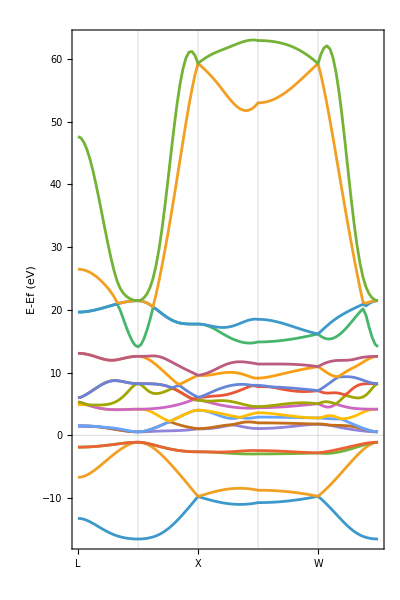

```mathematica
bands[[1;;-1]]//ListPlot[#,
Joined->True,
Frame->True,
FrameLabel->{None,"E-Ef (eV)"},
GridLines->{{21,41,61,81},{0}},
FrameTicks->{{{1,"L"},{21,"Γ"},{41,"X"},{61,"K"},{81,"W"},{101,"Γ"}},True},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotRange->{{1,101},All},
Axes->False,
AspectRatio->1.5
]&
```

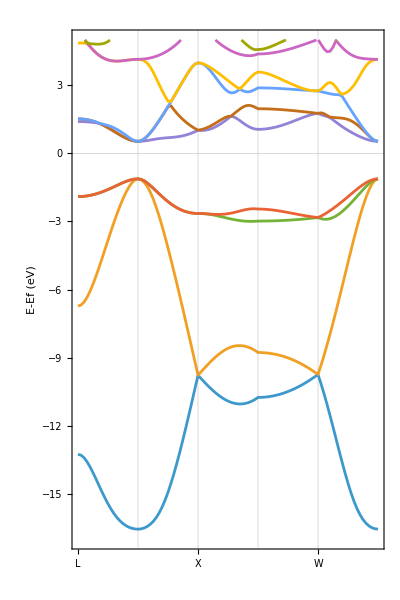

```mathematica
bands[[1;;-1]]//ListPlot[#,
Joined->True,
Frame->True,
FrameLabel->{None,"E-Ef (eV)"},
GridLines->{{21,41,61,81},{0}},
FrameTicks->{{{1,"L"},{21,"Γ"},{41,"X"},{61,"K"},{81,"W"},{101,"Γ"}},True},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotRange->{{1,101},{-17,5}},
Axes->False,
AspectRatio->1.5
]&
```

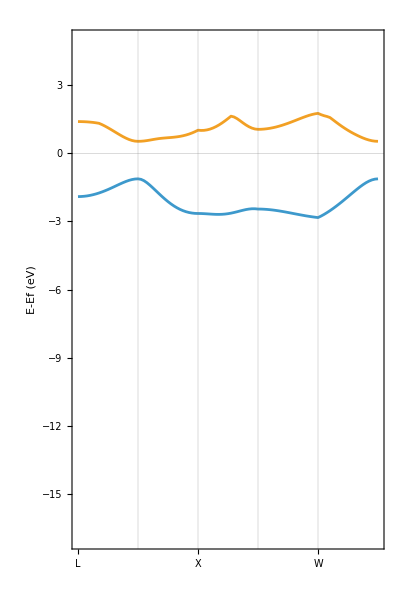

```mathematica
bands[[4;;5]]//ListPlot[#,
Joined->True,
Frame->True,
FrameLabel->{None,"E-Ef (eV)"},
GridLines->{{21,41,61,81},{0}},
FrameTicks->{{{1,"L"},{21,"Γ"},{41,"X"},{61,"K"},{81,"W"},{101,"Γ"}},True},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotRange->{{1,101},{-17,5}},
Axes->False,
AspectRatio->1.5
]&
```

Direct band, the highest value of the k space is the same as the lowest k value of the conduction band.  both are on the same gamma point. THis is incorrect, Si has indirect band, it has to be with the conservation of momentum and phonons.

compute the highest ocuppied band

```mathematica
hob = bands[[{4}]][[1]] //Interpolation[#]&(*stract the blue band/line*)
```

InterpolatingFunction[…]

```mathematica
lub = bands[[{5}]][[1]]//Interpolation[#]&
```

InterpolatingFunction[…]

```mathematica
FindMaximum[hob[x],{x,20}]
```

{-1.12135,{x→20.8439}}

```mathematica
FindMinimum[lub[x],{x,21}]
```

{0.532212,{x→21.1186}}

Then the bandgap E_g is

```mathematica
0.5322118605107021-(-1.121353548845205)
```

1.65357

The assigment is for the same as this notebook but for diamont.